# VE401 Recitation 4

## Descriptive Statistics

```mathematica
Data=Floor[RandomVariate[NormalDistribution[75,5],100]]
```

{77,79,68,71,79,81,80,76,74,73,69,73,70,70,71,79,81,75,82,77,71,77,79,72,81,69,71,80,71,77,75,73,75,73,75,72,74,83,86,82,67,68,72,80,70,70,76,78,71,70,74,81,72,68,72,80,77,78,87,80,81,73,73,72,79,74,76,78,73,72,76,79,71,73,81,71,75,75,76,76,59,74,71,79,66,77,87,76,71,74,77,69,80,77,64,70,79,65,70,71}

### Percentiles and Quartiles

Definitions: The x^th percentile is a value d_x of data such that x% of data are less than or equal to d_x. And,

The first quartile q_1 is the 25^th percentile.

The second quartile, or median, q_2 is the 50^th percentile.

The third quartile q_3 is the 75^th percentile.

Steps:

The median is q_2=Piecewise[{{1/2(x_(n/2)+x_(n/2+1)), if n is even}, {x_((n+1)/2), if n is odd}}], where x_i is the i^th smallest sample.

```mathematica
Median[Data]//N
```

74.5

The first quartile is

q_1=Piecewise[{{median of the smallest n/2 elements, if n is even}, {1/2(median of the smallest (n-1)/2  elements+median of the smallest (n+1)/2  elements), if n is odd}}]

The third quartile is

q_3=Piecewise[{{median of the largest n/2 elements, if n is even}, {1/2(median of the largest (n-1)/2  elements+median of the largest (n+1)/2  elements), if n is odd}}]

```mathematica
{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3]}=Quartiles[Data]//N
```

{71.,74.5,79.}

The interquartile range is calculated using IQR=q_3-q_1.

```mathematica
IQR=InterquartileRange[Data]
```

8

Example:

##### Given the set of data {1,2,3,4,5}, calculate its quartiles q_1,q_2,q_3 and interquartile range.

We have the first quartile q_1=((1+2)/2+2)/2=7/4, second quartile q_2=3, third quartile q_3=((4+5)/2+4)/2=17/4. The interquartile range is then IQR=5/2.

### Histograms

Steps: Note that in the exam you have to draw all diagrams using pencil and paper!

Choose a convenient number of bins k and a good bin width h. The bin width is calculated as

h=Piecewise[{{(max{x_i}-min{x_i})/(⌈log_2 n⌉+1), if using Sturges' rule}, {(2·IQR)/n^(1/3), if using Freedman·Diaconis Rule}}]

We usually round h up so that it is “nicer” for our data.

```mathematica
kSturges=Ceiling[Log2[Length[Data]]]+1
```

8

```mathematica
hSturges=Ceiling[(Max[Data]-Min[Data])/kSturges]
```

4

```mathematica
hFreedmanDiaconis=Ceiling[(2×InterquartileRange[Data])/CubeRoot[Length[Data]]]
```

4

Take the smallest datum, subtract one-half of the smallest decimal of the data, and successively add the bin width to obtain the bins.

```mathematica
bins=Table[Min[Data]-0.5+i×hSturges,{i,0,kSturges}]
```

{58.5,62.5,66.5,70.5,74.5,78.5,82.5,86.5,90.5}

Count the number of data in each bin and plot the histogram

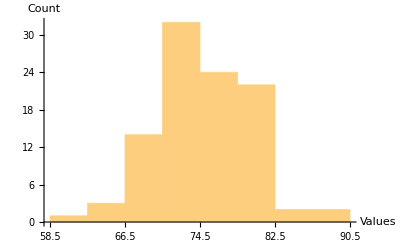

```mathematica
Histogram[Data,{Min[bins],Max[bins],hSturges},Ticks->{bins,Automatic},AxesLabel->{Values,Count}]
```

### Stem-and-Leaf Diagrams

Purpose: to get a rough idea of the shape of distribution.

Steps:

Choose a convenient number of leading decimal digits as stem.

Label each row with stem.

For each datum, note down the digit following the stem.

```mathematica
Floor[Sort[Data]]
```

{59,64,65,66,67,68,68,68,69,69,69,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,72,72,72,72,72,72,72,73,73,73,73,73,73,73,73,74,74,74,74,74,74,75,75,75,75,75,75,76,76,76,76,76,76,76,77,77,77,77,77,77,77,77,78,78,78,79,79,79,79,79,79,79,79,80,80,80,80,80,80,81,81,81,81,81,81,82,82,83,86,87,87}

```mathematica
Needs["StatisticalPlots`"]
StemLeafPlot[Floor[Data,1],IncludeStemCounts->True,IncludeEmptyStems->True, StemExponent->{1,"UnitDivisions"->2}]
```

Stem | Leaves | Counts
5 | 9 | 1
6 | 4 | 1
6 | 567888999 | 9
7 | 000000011111111111222222233333333444444 | 39
7 | 55555566666667777777788899999999 | 32
8 | 000000111111223 | 15
8 | 677 | 3
Stem units: 10

### Box plots

Steps:

Calculate inner fences f_1=q_1-3/2 IQR, and f_3=q_3+3/2 IQR.

```mathematica
Subscript[f, 1]=Subscript[Q, 1]-1.5IQR
Subscript[f, 3]=Subscript[Q, 3]+1.5IQR
```

59.

91.

Calculate outer fences F_1=q_1-3IQR and F_3=q_3+3IQR.

```mathematica
Subscript[F, 1]=Subscript[Q, 1]-3IQR
Subscript[F, 3]=Subscript[Q, 3]+3IQR
```

47

103

Calculate adjacent values a_1=min{x_k:x_k≥f_1}, and a_3=max{x_k:x_k≤f_3}

```mathematica
Subscript[a, 1]=Min[Select[Data,#≥Subscript[f, 1] &]]
Subscript[a, 3]=Max[Select[Data,#≤Subscript[f, 3] &]]
```

59

87

Data points in (F_1,f_1)∪(f_3,F_3) are near outliers and data points in (-∞,F_1)∪(F_3,∞) are far outliers.

```mathematica
nearoutliers=Select[Data,(Subscript[F, 1]<#<Subscript[f, 1])||(Subscript[f, 3]<#<Subscript[F, 3]) &]
```

{}

```mathematica
faroutliers=Select[Data,(Subscript[F, 1]>#)||(#>Subscript[F, 3]) &]
```

{}

```mathematica
outliers:=Join[nearoutliers,faroutliers]
```

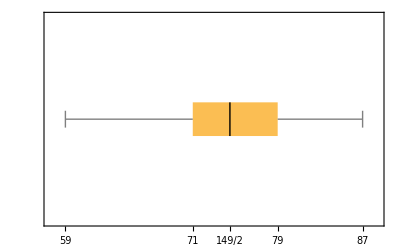

```mathematica
BoxWhiskerChart[Data,{"Outliers",{"MedianMarker",1,Directive[Black]}},BarOrigin->Left,FrameTicks->{{{},{}},{Join[Quartiles[Data],{Subscript[a, 1],Subscript[a, 3]},outliers],{}}}]
```

## Estimation

### Sample Statistics

random variables X_1,X_2,...,X_n are random samples of size n from the distribution X. They are independent identically distributed (i.i.d.) random variables.

| Sample | Actual
Range | max_(1≤k≤n) X_k-min_(1≤k≤n) X_k | Piecewise[{{Ω, if discrete}, {ℝ, if continuous}}]
Mean | X̄=1/n∑_(k=1)^n X_k | E[X]
Median | x̃=Piecewise[{{1/2(x_(n/2)+x_(n/2+1)), n even}, {x_((n+1)/2), n odd}}]
where x_i is the i^th smallest sample | m such that P[X≤m]=1/2
Variance | S^2=1/(n-1)∑_(k=1)^n (X_k-X̄)^2 | σ^2=E[(X-E[X])^2]
Standard Deviation | S=√(S^2) | σ=√(σ^2)

### Bias and Mean Square Error

Purpose: In order to have a “good” estimator θ̂ of the parameter θ, we want it to be

unbiased, or E[θ̂]=θ, and

Var[θ̂]→0 when n→∞.

Definitions: We define bias:=θ-E[θ̂], and mean square error MSE(θ̂):=E[(θ̂-θ)^2]=Var[θ̂]+(bias)^2.

Example:

##### Prove that the estimator of mean X̄=1/n∑_(k=1)^n X_k→μ as n→∞.

We have MSE(X̄)=E[(X̄-μ)^2]=Var[X̄]+μ-E[X̄]=σ^2/n+0⟶^(n→∞)0. Therefore X̄⟶^(n→∞)μ. This shows that the estimator is consistent.

### Method of Moments

Intuition: Given that the estimator for the k^th (k≥1) moment

OverHat[E[X^k]]=1/n∑_(i=1)^n X_i^k

is unbiased, we can use this to give good estimators for parameters that involve moments.

Steps:

Express the parameter in terms of moments. Hint: calculate E[X], E[X^2],...

Replace the moments with the corresponding estimators.

Example:

##### Provide a method of moment estimator of parameter p in the binomial distribution.

We have E[X]=n p and Var[X]=n p (1-p), therefore

Var[X]/E[X]=1-p⇒p=1-(E[X^2]-E[X]^2)/E[X]⇒p̂=1-(1/k∑_(i=1)^k X_i^2-(X̄)^2)/(X̄)=(X̄-1/k∑_(i=1)^k (X_i-X̄)^2)/(X̄).

### Method of Maximum Likelihood

Intuition: we want the parameter to be something, such that it will be the most likely to obtain our data set.

```mathematica
Manipulate[
Plot[PDF[NormalDistribution[μ,σ],x],{x,60,90},
PlotRange->{0,0.2},
Filling->Bottom,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"How likely will we have a sample x=75 when μ="<>ToString[μ]<>",σ="<>ToString[σ],
Epilog->{Directive[Red,Dotted,Thick],Line[{{75,0},{75,PDF[NormalDistribution[μ,σ],75]}}],PointSize[Large],Point[{75,PDF[NormalDistribution[μ,σ],75]}]}
],{μ,50,100},{σ,2,10},
Paneled->False]
```

```mathematica
DataSet=Data[[1;;10]];
Manipulate[
Plot[PDF[NormalDistribution[μ,σ],x],{x,50,100},
PlotRange->{0,0.2},
Filling->Bottom,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"How likely will we have the data when μ="<>ToString[μ]<>",σ="<>ToString[σ],
Epilog->{Directive[Red,Dotted,Thick],PointSize[Large],Point[Table[{i,PDF[NormalDistribution[μ,σ],i]},{i,DataSet}]]}
],{μ,50,100},{σ,2,10},
Paneled->False]
```

Mathematical representation:

likelihood of obtaining data set=∏_(i=1)^n likelihood of obtaining the data x_i
=∏_(i=1)^n f_X_θ(x_i)

Steps:

Calculate L(θ)=∏_(i=1)^n f_X_θ(x_i), and sometimes ln L(θ)=∑_(i=1)^n ln f_X_θ(x_i).

Find maximum of this likelihood by solving (∂ln L(θ))/(∂θ)=0.

Example:

##### Calculate the MLE for parameter μ,σ in normal distribution.

We have

ln L(μ,σ)=∑_(i=1)^n ln (1/(√(2π)σ)e^(-1/2((x_i-μ)/σ)^2))=∑_(i=1)^n [ln (1/(√(2π)σ))+-1/2((x_i-μ)/σ)^2]=n ln (1/(√(2π)σ))-1/(2 σ^2)∑_(i=1)^n (x_i-μ)^2

Now, calculating partial derivatives,

(∂ln L(μ,σ))/(∂μ)=1/(2 σ^2)∑_(i=1)^n 2(x_i-μ)=0⇒∑_(i=1)^n x_i=n μ⇒μ̂=1/n∑_(i=1)^n x_i=X̄

and

(∂ln L(μ,σ))/(∂σ)=-n/σ+1/σ^3∑_(i=1)^n (x_i-μ)^2=0⇒n σ^2=∑_(i=1)^n (x_i-μ)^2⇒(σ̂)^2=1/n∑_(i=1)^n (x_i-μ)^2

## Interval Estimation

### Confidence Interval with confidence level 100(1-α)%

Intuition: We need an interval such that in 100(1-α)% of the cases, the true value lies in the interval.

Mathematical representation: We calculate L_1,L_2 such that P[θ<L_1]=P[θ>L_2]=α/2, in this case P[L_1≤θ≤L_2]=1-α.

### Student T Distribution

Purpose: to describe the distribution T_γ=Z/(√(χ_γ^2/γ)).

Parameter: γ∈{1,2,...} is the degree of freedom.

PDF: f_T_γ(t)=(Γ((γ+1)/2))/(Γ(γ/2)√πγ)(1+t^2/γ)^(-(γ+1)/2).

```mathematica
Manipulate[
Plot[{PDF[StudentTDistribution[Floor[γ]],x],PDF[NormalDistribution[],x]},{x,-5,5},
PlotRange->{0,0.5},
Filling->Bottom,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Student T Distribution with γ="<>ToString[Floor[γ]],
PlotLegends->{"Student T Distribution","Standard Normal"}
],{γ,1,20},
Paneled->False]
```

### Confidence Interval for the Mean

Distribution of X_i | Sample 
size n | Variance σ^2 | Statistic | 1-α two-sided
confidence interval
X_i \[Distributed] N(μ,σ) | any | known | (X̄-μ)/(σ/√n)\[Distributed]N(0,1) | [X̄-z_(α/2)σ/(√n),X̄+z_(α/2)σ/(√n)]
X_i\[Distributed]any distribution | large | known | (X̄-μ)/(σ/√n)\[Distributed]N(0,1) | [X̄-z_(α/2)σ/(√n),X̄+z_(α/2)σ/(√n)]
X_i\[Distributed]any distribution | large | unknown | (X̄-μ)/(S/√n)\[Distributed]N(0,1) | [X̄-z_(α/2)S/(√n),X̄+z_(α/2)S/(√n)]
X_i \[Distributed] N(μ,σ) | small | unknown | (X̄-μ)/(S/√n)\[Distributed]t_(n-1) | [X̄-t_(α/2,n-1)S/(√n),X̄+t_(α/2,n-1)S/(√n)]
X_i\[Distributed]any distribution | small | known or 
unknown | Go home! | Go home!
(Source: https://stanford.edu/~shervine/teaching/cme-106/cheatsheet-statistics)

```mathematica
Subscript[z, α_]:=InverseCDF[NormalDistribution[],α]
```

```mathematica
Subscript[z, 0.95]
```

1.64485

### Confidence Interval for the Variance

Let X_1,...,X_n, n≥2, be a random sample of size n from a normal distribution with mean μ and variance σ^2, then

The sample mean X̄ is independent of the sample variance S^2,

X̄ is normally distributed with mean μ and variance σ^2/n,

(n-1)S^2/σ^2 is chi-squared distributed with n-1 degrees of freedom.

Distribution of X_i | Sample 
size n | Variance σ^2 | Statistic | 1-α two-sided
confidence interval
X_i \[Distributed] N(μ,σ) | any | known or
unknown | ((n-1)S^2)/σ^2\[Distributed]χ_(n-1)^2 | [((n-1)S^2)/(χ_(1-α/2,n-1)^2),((n-1)S^2)/(χ_(α/2,n-1)^2)]

## Problems in the Assignment

### A Tricky Question Involving the Binomial Distribution

A mathematics textbook has 200 pages on which typographical errors in the equations could occur. Suppose there are in fact five errors randomly dispersed among these 200 pages.

What is the probability that a random sample of 50 pages will contain at least one error?

How large must the random sample be to assure that at least three errors will be found with 90% probability?

#### Solution

We define “success” as “an error is in the sample”. p=P[the error is in the sample]=50/200=1/4. The total number of trial n=5. So P[at least one error]=1-P[X=0]=1-(5
0)(1/4)^0(3/4)^5=0.763.

Using normal approximation, P[X≥3]=1-P[X≤2]=1-Φ((2+1/2-5 p)/(√(5 p (1-p))))≥90%⇒Φ((2+1/2-5 p)/(√(5 p (1-p))))≤10%,

```mathematica
InverseCDF[NormalDistribution[],0.1]
```

-1.28155

(2+1/2-5 p)/(√(5 p (1-p)))≤-1.28⇒p≈0.748⇒the number of samples will be 200 p≈150.

### Linear Combination of Two Normal Distribution

Let X_1 and X_2 be independent normal distributions with means μ_1 and μ_2, and variance σ_1 and σ_2, respectively. Let λ_1,λ_2∈ℝ, Show that the linear combination Y=λ_1 X_1+λ_2 X_2 follows a normal distribution.

#### Solution

The moment generating function of λ_1 X_1 is

m_(λ_1 X_1)(t)=E[e^(t λ_1 X_1)]
=m_X_1(λ_1 t)
=exp(μ_1 λ_1 t+σ_1^2 λ_1^2 t^2/2)

And similar for λ_2 X_2. Since X_1 and X_2 are independent, λ_1 X_1,λ_2 X_2 are also independent and therefore

m_Y(t)=m_(λ_1 X_1)(t)m_(λ_2 X_2)(t)
=exp(μ_1 λ_1 t+(σ_1^2 λ_1^2 t^2)/2+μ_2 λ_2 t+(σ_2^2 λ_2^2 t^2)/2)
=exp[(μ_1 λ_1+μ_2 λ_2)t+((σ_1^2 λ_1^2+σ_2^2 λ_2^2)t^2)/2]

We notice that this is actually the MGF for normal distribution for μ=μ_1 λ_1+μ_2 λ_2 and σ^2=σ_1^2 λ_1^2+σ_2^2 λ_2^2. By the uniqueness of MGF we conclude that Y actually follows the same distribution.